```mathematica
CountryData[All, "Properties"]
```

{AdultPopulation,AgriculturalProducts,AgriculturalValueAdded,Airports,AlternateNames,AlternateStandardNames,AMRadioStations,AnnualBirths,AnnualDeaths,AnnualHIVAIDSDeaths,ArableLandArea,ArableLandFraction,Area,BirthRateFraction,BorderingCountries,BordersLengths,BoundaryLength,CallingCode,CapitalCity,CapitalLocation,CapitalLocationLink,CellularPhones,CenterCoordinates,CenterLocationLink,ChildPopulation,Classes,ClimateTypes,CoastlineLength,ConstructionValueAdded,Continent,Coordinates,Countries,CountryCode,CropsLandArea,CropsLandFraction,CurrencyCode,CurrencyName,CurrencyShortName,CurrencyUnit,CurrentAccountBalance,DeathRateFraction,Dependencies,DependencyParent,EconomicAid,ElderlyPopulation,ElectricalGridFrequency,ElectricalGridPlugImages,ElectricalGridPlugs,ElectricalGridSocketImages,ElectricalGridSockets,ElectricalGridVoltages,ElectricityConsumption,ElectricityExports,ElectricityImports,ElectricityProduction,EnvironmentalAgreements,EnvironmentalIssues,EthnicGroups,EthnicGroupsFractions,ExchangeRate,ExpenditureFractions,ExportCommodities,ExportPartners,ExportPartnersFractions,ExportValue,ExternalDebt,FemaleAdultPopulation,FemaleChildPopulation,FemaleElderlyPopulation,FemaleInfantMortalityFraction,FemaleLifeExpectancy,FemaleLiteracyFraction,FemaleMedianAge,FemalePopulation,FiscalYearDate,FixedInvestment,Flag,FlagDescription,FMRadioStations,ForeignExchangeReserves,ForeignOwnedShips,ForeignRegisteredShips,FullCoordinates,FullName,FullNativeName,FullPolygon,GDP,GDPAtParity,GDPPerCapita,GDPRealGrowth,GDPSectorFractions,GiniIndex,GovernmentConsumption,GovernmentDebt,GovernmentExpenditures,GovernmentReceipts,GovernmentSurplus,GrossInvestment,Groups,HighestElevation,HighestPoint,HIVAIDSDeathRateFraction,HIVAIDSFraction,HIVAIDSPopulation,HouseholdConsumption,ImportCommodities,ImportPartners,ImportPartnersFractions,ImportValue,IndependenceDate,IndependenceYear,IndustrialProductionGrowth,IndustrialValueAdded,InfantMortalityFraction,InfectiousDiseases,InflationRate,InternationalOrganizations,InternationalOrganizationsObserver,InternetCode,InternetHosts,InternetUsers,InventoryChange,IrrigatedLandArea,IrrigatedLandFraction,ISOName,LaborForce,LandArea,Languages,LanguagesDialects,LanguagesFractions,LargestCities,LifeExpectancy,LiteracyFraction,LowestElevation,LowestPoint,MajorIndustries,MajorPorts,MaleAdultPopulation,MaleChildPopulation,MaleElderlyPopulation,MaleInfantMortalityFraction,MaleLifeExpectancy,MaleLiteracyFraction,MaleMedianAge,MalePopulation,ManufacturingValueAdded,MaritimeClaims,MedianAge,Memberships,MerchantShips,MerchantShipsDeadWeight,MerchantShipsGross,MerchantShipTypes,MigrationRateFraction,MilitaryAgeFemales,MilitaryAgeMales,MilitaryAgePopulation,MilitaryAgeRate,MilitaryExpenditureFraction,MilitaryExpenditures,MilitaryFitFemales,MilitaryFitMales,MilitaryFitPopulation,MiscellaneousValueAdded,Name,NationalIncome,NationalityName,NativeName,NaturalGasConsumption,NaturalGasExports,NaturalGasImports,NaturalGasProduction,NaturalGasReserves,NaturalHazards,NaturalResources,OilConsumption,OilExports,OilImports,OilProduction,OilReserves,PavedAirportLengths,PavedAirports,PavedRoadLength,PhoneLines,Pipelines,Polygon,Population,PopulationGrowth,PovertyFraction,PriceIndex,RadioStations,RailwayGaugeLengths,RailwayGaugeRules,RailwayLength,RegionNames,Regions,Religions,ReligionsFractions,RoadLength,SchematicCoordinates,SchematicPolygon,SectorLaborFractions,Shape,ShortWaveRadioStations,SignedEnvironmentalAgreements,StandardName,SuffrageType,TelevisionStations,TerrainTypes,TimeZones,TotalConsumption,TotalFertilityRate,TradeValueAdded,TransportationValueAdded,UNCode,UnemploymentFraction,UNNumber,UnpavedAirportLengths,UnpavedAirports,UnpavedRoadLength,ValueAdded,WaterArea,WaterwayLength}

```mathematica
countryList = {Entity["Country","UnitedStates"], Entity["Country","Moldova"], Entity["Country","Brazil"], Entity["Country","China"], Entity["Country","Russia"], Entity["Country","Sweden"], Entity["Country","France"], Entity["Country","Japan"]};
propertyList = {"LandArea","ArableLandArea","CropsLandArea","ArableLandFraction","CropsLandFraction"};
dataOnly=Outer[#1[#2]&, countryList,propertyList];
For[i=1,i<=Length[countryList],i++,PrependTo[dataOnly⟦i⟧,countryList⟦i⟧]];
PrependTo[propertyList, ""];
PrependTo[dataOnly, propertyList];
TableForm[dataOnly]
```

| LandArea | ArableLandArea | CropsLandArea | ArableLandFraction | CropsLandFraction
United States | 9.16192×10^6 km^2 | 1.57737×10^6 km^2 | 19240. km^2 | 17.2439 % | 0.21 %
Moldova | 32891. km^2 | 16817. km^2 | 2897.7 km^2 | 51.1384 % | 8.81 %
Brazil | 8.45942×10^6 km^2 | 557620. km^2 | 75288.8 km^2 | 6.67158 % | 0.89 %
China | 9.32641×10^6 km^2 | 1.19489×10^6 km^2 | 118445. km^2 | 12.6782 % | 1.27 %
Russia | 16377742 km^2 | 1.21649×10^6 km^2 | 18695.4 km^2 | 7.4281 % | 0.11 %
Sweden | 410335. km^2 | 25500. km^2 | 41. km^2 | 6.26059 % | 0.01 %
France | 549970. km^2 | 181264. km^2 | 11076.3 km^2 | 33.1041 % | 2.03 %
Japan | 374744. km^2 | 41420. km^2 | 3372.7 km^2 | 11.3635 % | 0.9 %

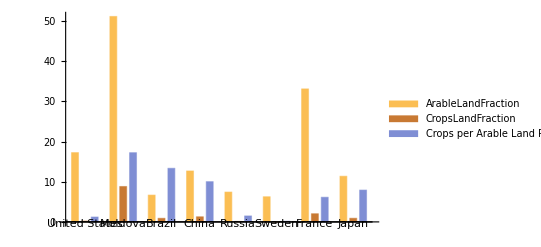

```mathematica
percentageProperties = {"ArableLandFraction","CropsLandFraction"};
percentageData=Outer[#1[#2]&, countryList,percentageProperties];
For[i=1,i<=Length[percentageData],i++,AppendTo[percentageData⟦i⟧,100*percentageData⟦i⟧⟦2⟧/percentageData⟦i⟧⟦1⟧]];
BarChart[percentageData, ChartLabels->{countryList, None}, ChartLegends->Append[percentageProperties,"Crops per Arable Land Ratio"]]
```

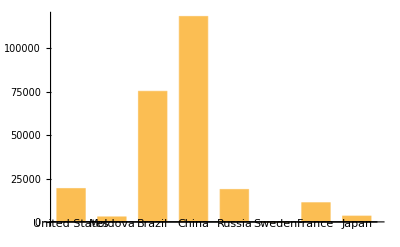

```mathematica
actualProperties = {"CropsLandArea"};
actualData=Outer[#1[#2]&, countryList,actualProperties];
BarChart[actualData, ChartLabels->{countryList, None}]
```

```mathematica
data =Table[{i,CountryData[i,"LandArea"],CountryData[i,"ArableLandArea"],CountryData[i,"CropsLandArea"],CountryData[i,"ArableLandFraction"], CountryData[i, "CropsLandFraction"]},{i, CountryData[All]}];
```

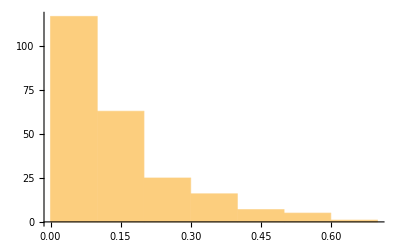

```mathematica
Histogram[data⟦All,5⟧]
```

```mathematica
dataNorthAmerica=DeleteCases[Table[{i,CountryData[i,"LandArea"],CountryData[i,"ArableLandArea"],CountryData[i,"CropsLandArea"],CountryData[i,"ArableLandFraction"], CountryData[i, "CropsLandFraction"]},{i,CountryData["NorthAmerica"]}],{_,_Missing,_Missing,_Missing,_Missing}];
dataAsia=DeleteCases[Table[{i,CountryData[i,"LandArea"],CountryData[i,"ArableLandArea"],CountryData[i,"CropsLandArea"],CountryData[i,"ArableLandFraction"], CountryData[i, "CropsLandFraction"]},{i,CountryData["Asia"]}],{_,_Missing,_Missing,_Missing,_Missing}];
dataEurope=DeleteCases[Table[{i,CountryData[i,"LandArea"],CountryData[i,"ArableLandArea"],CountryData[i,"CropsLandArea"],CountryData[i,"ArableLandFraction"], CountryData[i, "CropsLandFraction"]},{i,CountryData["Europe"]}],{_,_Missing,_Missing,_Missing,_Missing}];
dataAfrica=DeleteCases[Table[{i,CountryData[i,"LandArea"],CountryData[i,"ArableLandArea"],CountryData[i,"CropsLandArea"],CountryData[i,"ArableLandFraction"], CountryData[i, "CropsLandFraction"]},{i,CountryData["Africa"]}],{_,_Missing,_Missing,_Missing,_Missing}];
dataSouthAmerica=DeleteCases[Table[{i,CountryData[i,"LandArea"],CountryData[i,"ArableLandArea"],CountryData[i,"CropsLandArea"],CountryData[i,"ArableLandFraction"], CountryData[i, "CropsLandFraction"]},{i,CountryData["SouthAmerica"]}],{_,_Missing,_Missing,_Missing,_Missing}];
```

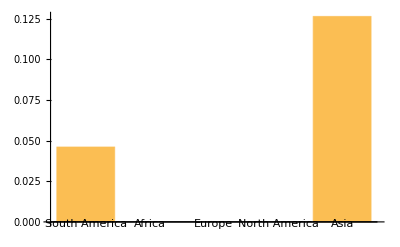

```mathematica
BarChart[{Mean[dataSouthAmerica⟦All,5⟧],Mean[dataAfrica⟦All,5⟧],Mean[dataEurope⟦All,5⟧],Mean[dataNorthAmerica⟦All,5⟧],Mean[dataAsia⟦All,5⟧]}, ChartLabels->{"South America","Africa","Europe","North America","Asia"}]
```

```mathematica
Mean[dataNorthAmerica⟦All,5⟧]
```

1/38 (3.98752+2 Missing[NotAvailable])